# Azterketa Praktika

## by Lucia Del Rio

```mathematica
Clear["Global`*"]
```

## 1.Praktikako birpasa

### 1. Ariketa

```mathematica
Table[Sqrt[8 i], {i,1,50}]
```

{2 √2,4,2 √6,4 √2,2 √10,4 √3,2 √14,8,6 √2,4 √5,2 √22,4 √6,2 √26,4 √7,2 √30,8 √2,2 √34,12,2 √38,4 √10,2 √42,4 √11,2 √46,8 √3,10 √2,4 √13,6 √6,4 √14,2 √58,4 √15,2 √62,16,2 √66,4 √17,2 √70,12 √2,2 √74,4 √19,2 √78,8 √5,2 √82,4 √21,2 √86,4 √22,6 √10,4 √23,2 √94,8 √6,14 √2,20}

### 2. Ariketa

```mathematica
g[x_,y_]=Cos[Power[x,3]+Power[y,3]]/(x-y+1);
```

```mathematica
f[x_]=Power[x,3]-2 x+1;
```

```mathematica
h[x_]=Power[x,2]-3 x+2;
```

#### a)

```mathematica
g[Pi,2 Pi]
g[Pi,2 Pi]//N
```

Cos[9 π^3]/(1-π)

0.399233

#### b)

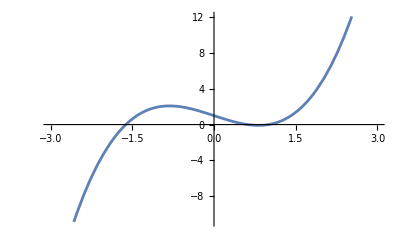

```mathematica
Plot[f[x],{x,-3,3}]
```

#### c)

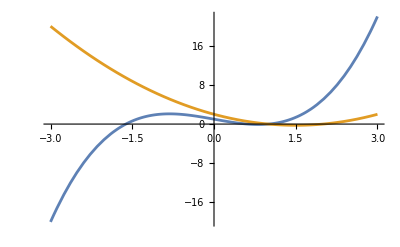

```mathematica
Plot[{f[x],h[x]},{x,-3,3}]
```

### 3.Ariketa

```mathematica
c={{4,1,3,1,3},{2,6,3,-1,2},{1,3,4,1,1},{-4,5,4,2,-3},{1,-1,-3,-1,2}}
```

{{4,1,3,1,3},{2,6,3,-1,2},{1,3,4,1,1},{-4,5,4,2,-3},{1,-1,-3,-1,2}}

```mathematica
MatrixForm[c]
```

(4 | 1 | 3 | 1 | 3
2 | 6 | 3 | -1 | 2
1 | 3 | 4 | 1 | 1
-4 | 5 | 4 | 2 | -3
1 | -1 | -3 | -1 | 2)

#### a)

```mathematica
Transpose[c[[3]]]
```

{1,3,4,1,1}

#### b)

```mathematica
Det[c[[{2,3,4,5},{1,2,4,5}]]]
```

-63

#### c)

```mathematica
Inverse[c]//MatrixForm
```

(91/120 | 7/24 | -4/3 | 5/24 | -9/20
41/120 | 5/24 | -2/3 | 7/24 | 1/20
-21/40 | -1/8 | 1 | -3/8 | -3/20
7/8 | -1/8 | -1 | 5/8 | 1/4
-67/120 | -7/24 | 4/3 | -5/24 | 13/20)

### 4.Ariketa

```mathematica
e={{1,1,1,1},{-m,1,1,2},{1,-m,1,3},{1,1,-m,4}};
```

```mathematica
MatrixForm[e]
```

(1 | 1 | 1 | 1
-m | 1 | 1 | 2
1 | -m | 1 | 3
1 | 1 | -m | 4)

#### a)

```mathematica
Flatten[e]
```

{1,1,1,1,-m,1,1,2,1,-m,1,3,1,1,-m,4}

#### b)

```mathematica
Solve[Det[e]==0,m]
```

{{m→-7},{m→-1},{m→-1}}

m/=-7 eta m/=-1 balioetarako SBD izango da beraz heina 4 izango da.

```mathematica
MatrixRank[e/.m->-7]
```

3

m = -7 baliorako heina 3 izango da.

```mathematica
MatrixRank[e/.m->-1]
```

2

m = -1 baliorako heina 2 izango da.

#### c)

```mathematica
Inverse[e/.m->2]//MatrixForm
```

(1/3 | -8/27 | 1/27 | 1/27
1/3 | 2/27 | -7/27 | 2/27
1/3 | 1/9 | 1/9 | -2/9
0 | 1/9 | 1/9 | 1/9)

#### d)

```mathematica
MatrixPower[e/.m->-1,5]//MatrixForm
```

(778 | 778 | 778 | 2332
1037 | 1037 | 1037 | 3110
1296 | 1296 | 1296 | 3888
1555 | 1555 | 1555 | 4666)

### 5.Ariketa

```mathematica
d={{1,a,-1,1},{2,1,-a,2},{1,-1,-1,a-1}};
```

```mathematica
MatrixForm[d]
```

(1 | a | -1 | 1
2 | 1 | -a | 2
1 | -1 | -1 | -1+a)

#### a)

```mathematica
Minoreak=Minors[d,3]
```

{{2+a-a^2,-2+5 a-2 a^2,-4+4 a-a^2,2 a+a^2-a^3}}

```mathematica
Solve[Minoreak=={{0,0,0,0}},a]
```

{{a→2}}

a /= 2 denean, heina 3 izango da .

```mathematica
MatrixRank[d/.a->2]
```

2

a = 2 denean heina 2 izango da .

#### b)

```mathematica
d1=d/.a->3
```

{{1,3,-1,1},{2,1,-3,2},{1,-1,-1,2}}

```mathematica
azpimat=d1[[{2,3},{1,3}]]
```

{{2,-3},{1,-1}}

```mathematica
MatrixRank[azpimat]
```

2

#### c)

```mathematica
d2=d/.a->2
```

{{1,2,-1,1},{2,1,-2,2},{1,-1,-1,1}}

```mathematica
Minors[d2,2]
```

{{-3,0,0,-3,3,0},{-3,0,0,-3,3,0},{-3,0,0,-3,3,0}}

## 2.Praktikako birpasa

### 1. Ariketa

```mathematica
Reduce[{a x+y+z==0,x+a y+z==0,x+y+a z==0},{x,y,z}]
```

(a==1&&z==-x-y)||(a==-2&&y==x&&z==2 x-y)||(-2+a+a^2≠0&&x==0&&y==0&&z==-y)

```mathematica
Solve[-2+a+a^2==0,a]
```

{{a→-2},{a→1}}

a /= 1 eta a /= -2 denean, SBD da eta bere soluzioa x = 0, y = 0, z= 0.
a = 1 denean SBI da eta bere soluzioa z=-x-y non x,y∈R.
a=-2 denean SBI da eta bere soluzioa y = x eta z = 2x-y non x∈R.

### 2. Ariketa

```mathematica
a1={1,α,1};
a2={α,-1-2 α,α};
b={1,-1,α};
Reduce[x1*a1+x2*a2==b,{x1,x2}]
```

α==1&&x1==1/2&&x2==1/2

α = 1 denean SBD izango da eta bere soluzioa x1 = 1/2 eta x2 = 1/2
α /= 1 denean Sistema bateraezina izango da.

### 3. Ariketa

```mathematica
m={{2,0,4,6},{1,1,1,1},{-1,3,-5,-9}};
X={x,y,z,t};
b={-2,0,4};
Solve[m.X==b,X]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{z→1-2 x-3 y,t→-1+x+2 y}}

SBI da eta bere soluzioa z = 1 - 2 x - 3 y eta t = -1 + x + 2 y non x, yϵR

### 4. Ariketa

```mathematica
Reduce[{2 x+a y+z==7,x+a y+z+t==b,x+2 a y+t==-1,b x+a y==b},{x,y,z,t}]
```

((b==0||b==4)&&a==0&&x==(6-b)/2&&z==1+b&&t==1/2 (-8+b))||(-1+b≠0&&x==(3 (-2+b))/(2 (-1+b))&&a≠0&&y==(6-b-2 x)/(2 a)&&z==1/2 (8+b-2 x)&&t==-7+b+x)

a = 0 bada eta b = 0 edo b = 4 bada SBI izango da non x = (6 - b)/2, z = 1 + b eta t = 1/2 (-8 + b) eta yϵR den .
a /= 0 bada eta b /=1 denean SBD izango da non x=(3(-2+b))/(2(-1+b)), y=(6-b-2x)/2a, z=1/2(8+b-2x) eta t = -7+b+x den.

### 5. Ariketa

#### a)

```mathematica
Reduce[{a x-y-z==-1,a x+b y-z==-1,a x+y+b z==-1,a x+y+z==1},{x,y,z}]
```

(b==-1&&a==0&&y==0&&z==1)||(b==-1&&a≠0&&x==0&&y==0&&z==1)

b/=-1 denean Sistema bateraezina izango da.
b = -1 eta a = 0 denean SBI izango da non y = 0 , z = 1 eta xϵR den .
b==-1 eta a /= 0 denean SBD izango da non x=0,y=0 eta z=1 den.

#### b)

```mathematica
m={{a,-1,-1},{a,b,-1},{a,1,b},{a,1,1}};
am={{a,-1,-1,-1},{a,b,-1,-1},{a,1,b,-1},{a,1,1,1}};
```

SBD denean :

```mathematica
MatrixRank[m/.{b->-1,a->1}]
MatrixRank[am/.{b->-1,a->1}]
```

3

3

SBI denean :

```mathematica
MatrixRank[m/.{b->-1,a->0}]
MatrixRank[am/.{b->-1,a->0}]
```

2

2

SBateraezina :

```mathematica
MatrixRank[m/.{b->1,a->0}]
MatrixRank[am/.{b->1,a->0}]
```

2

3

## 3.Praktikako birpasa

## 4.Praktikako birpasa